## Attempts with predict and classify

## Trying to use File[]

```mathematica
imagesPath = NotebookDirectory[] <> "ResistorProject/Assets/Images/";
dataPath = NotebookDirectory[] <> "ResistorProject/Assets/ResistorData/";
```

```mathematica
filesByType[type_?StringQ] := Map[
	File[#]->type&,
	FileNames[{"*.jpg", "*.png"}, dataPath <> type <> "/"]
];
```

```mathematica
makeData[] := Flatten @ Map[
	filesByType,
	StringDrop[
		Select[FileNames["*",dataPath], DirectoryQ],
		StringLength[dataPath]
	]
];
```

```mathematica
data = RandomSample[makeData[]];
```

```mathematica
data[[1]]
```

File[/Users/carolinadelgadillo/Documents/GitHub/WSS2017/ResistorProject/Assets/ResistorData/470/IMG_7618.png]→470

```mathematica
Length[data]
```

397

```mathematica
trainingData = data[[;;300]];
testData = data[[301;;]];
```

```mathematica
getAllImages[x_]:=Map[
Import[Keys[{#}][[1]]]->ToExpression[Values[{#}][[1]]]&,
x
];
```

```mathematica
trainingSet = getAllImages[trainingData];
testSet = getAllImages[testData];
```

```mathematica
trainingSet[[1]]
```

-Graphics-→470

```mathematica
cNoParameters = Classify[trainingSet]
```

ClassifierFunction[…]

```mathematica
img = -Graphics-;
```

```mathematica
cNoParameters[resistorCrop[img],"Probabilities"]
```

<|10→0.000152788,470→0.00160622,4700→0.988533,220000→0.00970753|>

```mathematica
mask=DeleteSmallComponents[Binarize[ColorNegate@img,0.5]];
ans = ImageRotate[ImageTrim[img,#[[1]],20],#[[2]]+Pi/2,"SameRatioCropping"]&/@ComponentMeasurements[mask,{"BoundingBox","Orientation"}][[All,2]];
```

```mathematica
ans
```

{-Graphics-}

```mathematica
cNoParameters[ans,"Probabilities"]
```

{<|10→0.58544,470→0.000112739,4700→0.291202,220000→0.123246|>}

```mathematica
ClassifierInformation[cNoParameters]
```

Classifier information
Method | Logistic regression
Number of classes | 4
Number of features | 1
Number of training examples | 300
L1 regularization coefficient | 0
L2 regularization coefficient | 10.

```mathematica
cNoParametersM = ClassifierMeasurements[cNoParameters, testSet]
```

ClassifierMeasurementsObject[…]

```mathematica
cNoParametersM["Accuracy"]
```

0.814433

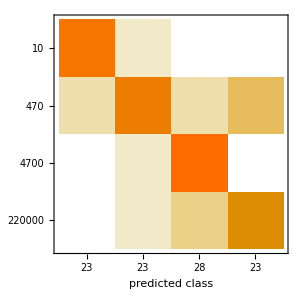

```mathematica
cNoParametersM["ConfusionMatrixPlot"]
```

```mathematica
cNeuralNet = Classify[trainingSet, Method->"NeuralNetwork", PerformanceGoal->"Quality"]
```

ClassifierFunction[…]

```mathematica
cNeuralNetM = ClassifierMeasurements[cNeuralNet, testSet]
```

ClassifierMeasurementsObject[…]

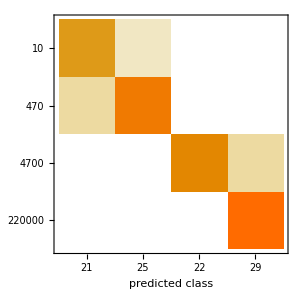

```mathematica
cNeuralNetM["ConfusionMatrixPlot"]
```

```mathematica
pNoParameters = Predict[trainingSet]
```

PredictorFunction[…]

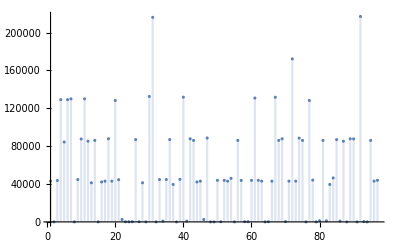

```mathematica
Show[
DiscretePlot[
Module[
{image, value},
image = Keys[testSet[[x]]];
value = Values[testSet[[x]]];
Abs[value - pNoParameters[image]]
],
{x, 1, Length[testSet], 1}
]
]
```